```mathematica
arrivalRateData=Import["D:\\School\\CS1538-Project\\data\\RAW-DATA.xlsx", {"Data",3,Range[4,63],11}];
DistributionFitTest[arrivalRateData, PoissonDistribution[3.5],"TestConclusion"]
```

The null hypothesis that the data is distributed according to the PoissonDistribution[3.5] is not rejected at the 5 percent level based on the Pearson χ^2 test.

```mathematica
queueServiceTime=Import["D:\\School\\CS1538-Project\\data\\RAW-DATA.xlsx",{"Data",2,Range[2,61],2}];
H =DistributionFitTest[queueServiceTime, NormalDistribution[97.78,79.80],"HypothesisTestData"];
```

```mathematica
H["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | -60. | 1.
Cramér-von Mises | 20. | 2.88658×10^-15
Jarque-Bera ALM | 354.043 | 0.
Mardia Combined | 354.043 | 0.
Mardia Kurtosis | 14.7337 | 3.91841×10^-49
Mardia Skewness | 63.5856 | 1.53549×10^-15
Pearson χ^2 | 60. | 3.6243×10^-9
Shapiro-Wilk | 0.782794 | 5.15611×10^-8

```mathematica
R=RandomVariate[d=NormalDistribution[97.78,79.80],60];
g=DistributionFitTest[R,d,"HypothesisTestData"];
```

```mathematica
g["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 2.76182 | 0.0364021
Cramér-von Mises | 0.492205 | 0.0416925
Jarque-Bera ALM | 5.68622 | 0.0663812
Kolmogorov-Smirnov | 0.141755 | 0.162766
Kuiper | 0.152086 | 0.329985
Mardia Combined | 5.68622 | 0.0663812
Mardia Kurtosis | 1.86809 | 0.0617498
Mardia Skewness | 0.401549 | 0.526291
Pearson χ^2 | 11.5 | 0.319911
Shapiro-Wilk | 0.975636 | 0.272413
Watson U^2 | 0.0833559 | 0.386761

```mathematica
Mean[queueServiceTime]
```

97.7833

```mathematica
StandardDeviation[queueServiceTime]
```

79.7998

```mathematica
test=DistributionFitTest[queueServiceTime,NormalDistribution[97.7833,79.7998],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
test["TestConclusion"]
```

0.121098[TestConclusion]

```mathematica
cashierServiceTime=Import["D:\\School\\CS1538-Project\\data\\RAW-DATA.xlsx",{"Data",2,Range[2,61],3}];
```

```mathematica
m=Mean[cashierServiceTime];
std=StandardDeviation[cashierServiceTime];
test = DistributionFitTest[cashierServiceTime,NormalDistribution[m,std],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
test["TestDataTable","KolmogorovSmirnov"]
```

DistributionFitTest::ties: Ties exist in the data and will be ignored for the {"KolmogorovSmirnov"} test, which assumes unique values.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.205821 | 0.0104746

```mathematica
KolmogorovSmirnovTest[cashierServiceTime,NormalDistribution[m,std],"ShortTestConclusion"]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the {"KolmogorovSmirnov"} test, which assumes unique values.

Reject

```mathematica
DistributionFitTest[cashierServiceTime,ExponentialDistribution[1./15.35],"HypothesisTestData"]
```

HypothesisTestData[…]

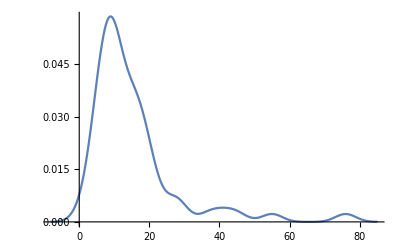

```mathematica
Show[SmoothHistogram[cashierServiceTime]]
```

```mathematica
StandardDeviation[cashierServiceTime]
```

12.9652

```mathematica
Mean[cashierServiceTime]
```

15.35

```mathematica
updatedCST=Import["D:\\School\\CS1538-Project\\data\\RAW-DATA.xlsx",{"Data",5,Range[1,53],1}];
```

```mathematica
DistributionFitTest[updatedCST,UniformDistribution[{2,28}],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
Mean[updatedCST]
```

12.0189

```mathematica
StandardDeviation[updatedCST]
```

5.68565

```mathematica
DistributionFitTest[updatedCST,NormalDistribution[12.018867924528301,5.685645102556139],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
normalCheckOut=Import["D:\\School\\CS1538-Project\\NormalCheckOut.txt","Data"];
```

```mathematica
mean=Mean[normalCheckOut]
```

{11893/1000}

```mathematica
std = StandardDeviation[normalCheckOut]
```

{(√(27647551/1110))/30}

```mathematica
normalCheckOut
```

{{15},{9},{8},{1},{15},{11},{18},{10},{8},{19},{23},{12},{12},{3},{8},{6},{19},{13},{12},{12},{12},{14},{19},{19},{16},{16},{6},{4},{9},{14},{18},{10},{13},{8},{3},{11},{15},{10},{12},{9},{19},{13},{21},{19},{4},{24},{8},{3},{10},{8},{18},{21},{15},{16},{8},{5},{18},{22},{7},{16},{8},{17},{15},{9},{10},{22},{16},{14},{12},{12},{24},{8},{11},{19},{13},{14},{5},{15},{14},{11},{20},{10},{4},{5},{13},{17},{12},{12},{2},{10},{4},{3},{6},{13},{8},{4},{18},{11},{16},{7},{8},{12},{9},{3},{14},{10},{4},{13},{13},{6},{11},{15},{17},{5},{6},{15},{14},{14},{9},{13},{12},{16},{23},{10},{19},{8},{5},{13},{11},{3},{14},{12},{14},{14},{13},{12},{12},{18},{7},{14},{12},{17},{23},{11},{12},{13},{16},{8},{15},{14},{13},{12},{4},{13},{13},{12},{16},{11},{13},{13},{10},{10},{12},{21},{13},{18},{25},{16},{8},{16},{20},{20},{7},{18},{18},{13},{6},{13},{15},{16},{14},{7},{2},{3},{13},{6},{6},{12},{7},{14},{6},{8},{15},{15},{5},{16},{12},{4},{18},{12},{11},{15},{7},{12},{12},{10},{9},{15},{17},{8},{7},{20},{9},{12},{15},{22},{18},{7},{24},{15},{9},{2},{10},{19},{10},{6},{20},{19},{9},{13},{14},{20},{8},{12},{10},{12},{17},{9},{6},{12},{8},{5},{14},{6},{6},{6},{24},{10},{20},{11},{11},{18},{2},{10},{3},{12},{6},{19},{17},{11},{7},{11},{6},{15},{13},{12},{16},{7},{11},{7},{14},{13},{11},{15},{10},{4},{9},{13},{12},{3},{7},{3},{11},{2},{10},{6},{18},{20},{7},{6},{18},{11},{9},{13},{18},{16},{17},{6},{18},{11},{3},{13},{9},{6},{13},{9},{14},{18},{13},{15},{19},{28},{12},{5},{8},{14},{24},{22},{25},{11},{10},{1},{11},{7},{11},{5},{8},{8},{9},{6},{20},{9},{9},{26},{8},{21},{10},{13},{13},{6},{16},{16},{12},{14},{10},{13},{9},{6},{5},{1},{15},{1},{8},{5},{14},{12},{14},{12},{13},{12},{18},{27},{10},{7},{15},{14},{9},{15},{19},{13},{4},{14},{12},{17},{17},{20},{17},{6},{10},{12},{10},{22},{11},{19},{11},{8},{10},{16},{19},{19},{15},{16},{11},{8},{5},{17},{7},{8},{11},{7},{14},{11},{12},{11},{16},{26},{18},{8},{11},{20},{13},{11},{11},{20},{16},{17},{8},{4},{3},{2},{11},{16},{12},{17},{16},{15},{6},{10},{6},{10},{8},{6},{15},{16},{13},{14},{19},{12},{12},{13},{12},{10},{16},{18},{10},{10},{4},{11},{7},{6},{15},{17},{14},{2},{4},{17},{13},{7},{8},{18},{7},{8},{11},{21},{13},{12},{18},{11},{20},{4},{7},{2},{12},{19},{8},{8},{12},{10},{10},{10},{13},{17},{21},{19},{9},{11},{20},{19},{3},{10},{12},{4},{24},{15},{2},{7},{10},{15},{16},{15},{13},{24},{3},{28},{16},{16},{14},{7},{6},{20},{12},{9},{23},{5},{23},{1},{9},{10},{15},{1},{15},{19},{9},{10},{9},{11},{6},{9},{8},{15},{16},{6},{20},{7},{9},{1},{8},{13},{14},{4},{13},{11},{3},{5},{15},{17},{15},{13},{15},{14},{7},{17},{18},{7},{13},{2},{12},{7},{21},{24},{16},{16},{13},{7},{9},{9},{12},{7},{2},{19},{5},{16},{16},{12},{14},{14},{8},{2},{9},{14},{2},{10},{11},{3},{11},{11},{17},{21},{10},{12},{15},{7},{3},{13},{16},{22},{16},{3},{12},{13},{17},{5},{12},{12},{11},{18},{14},{6},{15},{19},{15},{14},{14},{15},{16},{14},{13},{12},{18},{14},{20},{10},{25},{16},{17},{12},{10},{23},{18},{8},{18},{8},{17},{4},{12},{12},{14},{11},{16},{14},{17},{5},{12},{14},{12},{10},{8},{12},{19},{4},{15},{12},{9},{9},{19},{5},{20},{18},{14},{12},{23},{12},{12},{8},{8},{10},{16},{12},{2},{10},{14},{5},{16},{16},{13},{9},{4},{13},{17},{19},{11},{14},{14},{32},{17},{17},{7},{7},{15},{6},{4},{3},{12},{6},{19},{1},{9},{4},{9},{16},{8},{12},{13},{14},{15},{6},{17},{9},{11},{17},{7},{7},{15},{17},{6},{9},{6},{1},{15},{17},{8},{12},{9},{5},{12},{10},{13},{3},{9},{9},{12},{15},{12},{5},{10},{14},{10},{14},{5},{14},{1},{10},{18},{12},{14},{8},{15},{6},{9},{16},{11},{11},{6},{14},{23},{12},{7},{19},{9},{7},{14},{7},{8},{19},{7},{21},{16},{15},{10},{11},{15},{16},{7},{8},{7},{17},{1},{11},{2},{11},{25},{3},{17},{15},{13},{8},{15},{6},{10},{8},{9},{16},{13},{20},{9},{4},{12},{9},{12},{9},{16},{17},{12},{21},{13},{18},{10},{5},{8},{7},{15},{5},{11},{11},{6},{12},{14},{3},{15},{10},{12},{2},{5},{12},{2},{6},{11},{2},{7},{15},{14},{8},{16},{21},{8},{13},{8},{12},{10},{16},{19},{6},{9},{12},{10},{17},{11},{14},{16},{18},{8},{10},{3},{9},{7},{17},{14},{12},{13},{15},{11},{10},{8},{6},{14},{12},{10},{5},{11},{4},{10},{23},{14},{4},{14},{6},{11},{14},{12},{6},{8},{15},{7},{11},{13},{13},{10},{14},{15},{5},{13},{12},{14},{9},{12},{3},{4},{10},{12},{8},{13},{9},{13},{4},{8},{8},{8},{16},{4},{4},{22},{13},{4},{5},{11},{20},{4},{20},{12},{12},{11},{16},{14},{19},{19},{14},{8},{8},{8},{17},{10},{20},{15},{15},{10},{15},{5},{8},{18},{11},{9},{6},{22},{16},{15},{15},{6},{10},{14},{17},{12},{11},{22},{14},{21},{16},{11},{1},{9},{12},{23},{11},{4},{22},{6},{3},{9},{5},{14},{13},{9},{17},{26},{15},{12},{11},{16},{16},{12},{7},{16},{20},{7},{7},{9},{12},{15},{13},{17},{14},{19},{20},{12},{8},{27},{11},{16},{16},{13},{14}}

```mathematica
normalCheckOut=Import["D:\\School\\CS1538-Project\\NormalCheckOut.csv","Data"]
```

{{12,6,9,14,14,9,20,7,20,15,13,3,7,20,13,24,8,11,16,12,10,24,8,18,7,18,15,7,5,10,1,5,16,14,13,8,18,20,9,17,11,19,24,8,13,9,1,21,2,2,24,8,6,12,1,20,15,6,13,14,5,16,7,13,27,11,7,3,18,18,8,15,8,17,12,5,10,16,6,13,14,8,3,16,17,17,2,16,4,11,16,6,4,18,16,11,15,8,9,10,13,11,9,12,15,15,13,2,22,18,22,6,17,12,6,11,7,17,8,9,18,7,13,20,6,10,17,18,8,18,7,11,17,12,14,13,6,11,19,11,1,12,15,13,15,12,7,3,14,15,13,5,18,17,7,8,8,21,8,5,7,12,14,12,14,3,1,14,13,11,10,10,18,13,17,9,6,17,13,20,17,8,17,11,9,5,5,19,9,15,10,11,13,8,3,13,16,24,8,5,11,16,2,6,19,10,9,9,14,15,9,12,20,14,15,15,18,13,12,7,15,10,6,9,1,17,6,9,17,8,10,23,11,5,15,23,10,7,12,16,11,12,18,23,1,16,10,15,12,8,19,11,2,21,13,18,13,17,17,13,15,17,5,11,8,7,11,14,8,9,17,13,14,16,10,8,17,12,14,15,18,3,17,18,6,2,15,12,11,11,8,9,16,4,12,1,10,13,13,20,11,10,1,8,12,17,3,7,12,10,3,12,20,14,15,8,2,9,9,8,14,9,4,15,8,11,20,13,9,12,13,13,14,27,12,10,5,2,13,10,7,20,20,12,7,12,3,5,13,9,16,13,17,14,11,15,11,17,11,2,28,10,6,17,15,7,14,1,15,7,21,16,13,10,13,4,12,6,17,18,11,10,4,7,11,13,10,15,13,13,3,6,10,9,4,21,12,12,19,7,9,20,23,8,12,19,12,9,10,10,24,12,9,15,11,10,9,14,10,12,17,10,13,20,6,18,20,7,15,9,21,5,5,11,13,10,10,9,10,5,6,10,17,12,23,10,7,14,14,21,14,3,16,3,12,14,12,9,9,13,5,12,11,23,8,8,21,10,15,5,3,7,16,13,11,23,14,3,7,20,15,4,15,3,14,9,9,21,4,11,18,18,11,1,2,21,8,11,13,11,21,21,24,5,10,13,13,31,11,12,17,12,12,18,9,9,10,11,11,17,17,14,1,13,15,18,14,14,5,20,17,6,25,14,14,10,7,9,17,5,9,17,19,13,8,18,9,13,16,16,8,5,3,1,19,10,5,9,4,8,15,15,11,23,8,15,3,14,4,11,9,19,9,11,12,18,10,6,12,12,15,4,3,15,14,9,6,10,20,8,18,13,26,10,13,21,12,19,11,13,12,12,10,13,23,5,10,11,16,13,5,18,15,20,9,7,15,12,5,11,19,24,8,3,14,18,26,23,18,9,8,22,7,7,12,16,15,7,7,6,13,7,9,23,15,7,25,15,14,9,11,20,18,4,11,9,18,16,6,23,6,2,7,18,11,4,9,15,2,11,11,4,8,17,11,12,8,6,8,26,10,5,7,9,14,6,7,8,12,10,3,2,3,17,10,14,13,11,19,10,15,12,14,15,9,11,14,21,12,12,8,7,13,6,11,12,3,17,12,20,17,23,10,15,19,9,9,13,18,8,17,8,15,10,15,10,17,8,11,6,9,8,11,18,5,17,14,13,1,20,11,5,19,9,3,10,6,4,9,10,17,17,7,19,7,10,12,12,11,12,13,18,8,12,5,7,13,14,9,11,10,2,16,9,7,14,7,4,18,9,14,13,13,10,10,17,4,16,11,3,8,17,11,13,14,8,6,11,17,15,14,16,2,17,12,9,14,24,11,11,16,10,18,10,9,3,11,6,9,7,13,5,16,5,13,7,12,6,19,9,7,12,10,13,13,13,14,19,3,11,9,6,16,8,8,4,11,13,12,12,13,14,17,17,8,25,8,3,23,14,22,4,15,6,6,16,17,28,9,8,16,16,19,6,1,13,2,25,10,11,25,15,5,9,7,3,11,10,5,8,12,15,22,15,17,7,7,21,6,5,16,19,6,9,3,16,6,17,11,14,17,9,19,13,14,11,10,5,8,16,8,8,8,6,5,13,8,15,14,13,14,11,13,10,10,16,16,14,13,14,17,9,10,17,8,13,10,19,9,15,12,5,6,11,17,17,14,8,17,13,7,14,20,19,12,6,22,17,5,7,13,5,13,12,13,13,12,10,10,9,5,7,14,6,14,9,21,10,15,17,15}}

```mathematica
mean=Mean[normalCheckOut]
std=StandardDeviation[normalCheckOut];
DistributionFitTest[normalCheckOut,NormalDistribution[mean,std],"HypothesisTestData"];
```

12,6,9,14,14,9,20,7,20,15,13,3,7,20,13,24,8,11,16,12,10,24,8,18,7,18,15,7,5,10,1,5,16,14,13,8,18,20,9,17,11,19,24,8,13,9,1,21,2,2,24,8,6,12,1,20,15,6,13,14,5,16,7,13,27,11,7,3,18,18,8,15,8,17,12,5,10,16,6,13,14,8,3,16,17,17,2,16,4,11,16,6,4,18,16,11,15,8,9,10,13,11,9,12,15,15,13,2,22,18,22,6,17,12,6,11,7,17,8,9,18,7,13,20,6,10,17,18,8,18,7,11,17,12,14,13,6,11,19,11,1,12,15,13,15,12,7,3,14,15,13,5,18,17,7,8,8,21,8,5,7,12,14,12,14,3,1,14,13,11,10,10,18,13,17,9,6,17,13,20,17,8,17,11,9,5,5,19,9,15,10,11,13,8,3,13,16,24,8,5,11,16,2,6,19,10,9,9,14,15,9,12,20,14,15,15,18,13,12,7,15,10,6,9,1,17,6,9,17,8,10,23,11,5,15,23,10,7,12,16,11,12,18,23,1,16,10,15,12,8,19,11,2,21,13,18,13,17,17,13,15,17,5,11,8,7,11,14,8,9,17,13,14,16,10,8,17,12,14,15,18,3,17,18,6,2,15,12,11,11,8,9,16,4,12,1,10,13,13,20,11,10,1,8,12,17,3,7,12,10,3,12,20,14,15,8,2,9,9,8,14,9,4,15,8,11,20,13,9,12,13,13,14,27,12,10,5,2,13,10,7,20,20,12,7,12,3,5,13,9,16,13,17,14,11,15,11,17,11,2,28,10,6,17,15,7,14,1,15,7,21,16,13,10,13,4,12,6,17,18,11,10,4,7,11,13,10,15,13,13,3,6,10,9,4,21,12,12,19,7,9,20,23,8,12,19,12,9,10,10,24,12,9,15,11,10,9,14,10,12,17,10,13,20,6,18,20,7,15,9,21,5,5,11,13,10,10,9,10,5,6,10,17,12,23,10,7,14,14,21,14,3,16,3,12,14,12,9,9,13,5,12,11,23,8,8,21,10,15,5,3,7,16,13,11,23,14,3,7,20,15,4,15,3,14,9,9,21,4,11,18,18,11,1,2,21,8,11,13,11,21,21,24,5,10,13,13,31,11,12,17,12,12,18,9,9,10,11,11,17,17,14,1,13,15,18,14,14,5,20,17,6,25,14,14,10,7,9,17,5,9,17,19,13,8,18,9,13,16,16,8,5,3,1,19,10,5,9,4,8,15,15,11,23,8,15,3,14,4,11,9,19,9,11,12,18,10,6,12,12,15,4,3,15,14,9,6,10,20,8,18,13,26,10,13,21,12,19,11,13,12,12,10,13,23,5,10,11,16,13,5,18,15,20,9,7,15,12,5,11,19,24,8,3,14,18,26,23,18,9,8,22,7,7,12,16,15,7,7,6,13,7,9,23,15,7,25,15,14,9,11,20,18,4,11,9,18,16,6,23,6,2,7,18,11,4,9,15,2,11,11,4,8,17,11,12,8,6,8,26,10,5,7,9,14,6,7,8,12,10,3,2,3,17,10,14,13,11,19,10,15,12,14,15,9,11,14,21,12,12,8,7,13,6,11,12,3,17,12,20,17,23,10,15,19,9,9,13,18,8,17,8,15,10,15,10,17,8,11,6,9,8,11,18,5,17,14,13,1,20,11,5,19,9,3,10,6,4,9,10,17,17,7,19,7,10,12,12,11,12,13,18,8,12,5,7,13,14,9,11,10,2,16,9,7,14,7,4,18,9,14,13,13,10,10,17,4,16,11,3,8,17,11,13,14,8,6,11,17,15,14,16,2,17,12,9,14,24,11,11,16,10,18,10,9,3,11,6,9,7,13,5,16,5,13,7,12,6,19,9,7,12,10,13,13,13,14,19,3,11,9,6,16,8,8,4,11,13,12,12,13,14,17,17,8,25,8,3,23,14,22,4,15,6,6,16,17,28,9,8,16,16,19,6,1,13,2,25,10,11,25,15,5,9,7,3,11,10,5,8,12,15,22,15,17,7,7,21,6,5,16,19,6,9,3,16,6,17,11,14,17,9,19,13,14,11,10,5,8,16,8,8,8,6,5,13,8,15,14,13,14,11,13,10,10,16,16,14,13,14,17,9,10,17,8,13,10,19,9,15,12,5,6,11,17,17,14,8,17,13,7,14,20,19,12,6,22,17,5,7,13,5,13,12,13,13,12,10,10,9,5,7,14,6,14,9,21,10,15,17,15

StandardDeviation::shlen: The argument {"12,6,9,14,14,9,20,7,20,15,13,3,7,20,13,24,8,11,16,12,10,24,8,18,7,18,15,7,5,10,1,5,16,14,13,8,18,20,9,17,11,19,24,8,13,9,1,21,2,2,24,8,6,12,1,20,15,6,13,14,5,16,7,13,27,11,7,3,18,18,8,15,8,17,12,5,10,16,6,13,14,8,3,16,17,17,2,16,4,11,16,6,4,18,16,11,15,8,9,10,13,11,9,12,15,15,13,2,22,18,22,6,17,12,6,11,7,17,8,9,18,7,13,20,6,10,17,18,8,18,7,11,17,12,14,13,6,11,19,11,1,12,15,13,15,12,7,3,14,15,13,5,18,17,7,8,8,21,8" … "3,13,13,14,19,3,11,9,6,16,8,8,4,11,13,12,12,13,14,17,17,8,25,8,3,23,14,22,4,15,6,6,16,17,28,9,8,16,16,19,6,1,13,2,25,10,11,25,15,5,9,7,3,11,10,5,8,12,15,22,15,17,7,7,21,6,5,16,19,6,9,3,16,6,17,11,14,17,9,19,13,14,11,10,5,8,16,8,8,8,6,5,13,8,15,14,13,14,11,13,10,10,16,16,14,13,14,17,9,10,17,8,13,10,19,9,15,12,5,6,11,17,17,14,8,17,13,7,14,20,19,12,6,22,17,5,7,13,5,13,12,13,13,12,10,10,9,5,7,14,6,14,9,21,10,15,17,15"} should have at least two elements.

DistributionFitTest::rctnln: The argument {"12,6,9,14,14,9,20,7,20,15,13,3,7,20,13,24,8,11,16,12,10,24,8,18,7,18,15,7,5,10,1,5,16,14,13,8,18,20,9,17,11,19,24,8,13,9,1,21,2,2,24,8,6,12,1,20,15,6,13,14,5,16,7,13,27,11,7,3,18,18,8,15,8,17,12,5,10,16,6,13,14,8,3,16,17,17,2,16,4,11,16,6,4,18,16,11,15,8,9,10,13,11,9,12,15,15,13,2,22,18,22,6,17,12,6,11,7,17,8,9,18,7,13,20,6,10,17,18,8,18,7,11,17,12,14,13,6,11,19,11,1,12,15,13,15,12,7,3,14,15,13,5,18,17,7,8,8,21,8" … "3,13,13,14,19,3,11,9,6,16,8,8,4,11,13,12,12,13,14,17,17,8,25,8,3,23,14,22,4,15,6,6,16,17,28,9,8,16,16,19,6,1,13,2,25,10,11,25,15,5,9,7,3,11,10,5,8,12,15,22,15,17,7,7,21,6,5,16,19,6,9,3,16,6,17,11,14,17,9,19,13,14,11,10,5,8,16,8,8,8,6,5,13,8,15,14,13,14,11,13,10,10,16,16,14,13,14,17,9,10,17,8,13,10,19,9,15,12,5,6,11,17,17,14,8,17,13,7,14,20,19,12,6,22,17,5,7,13,5,13,12,13,13,12,10,10,9,5,7,14,6,14,9,21,10,15,17,15"} at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

```mathematica
normalCheckOut={21.,9.,10.,8.,11.,12.,15.,11.,13.,18.,15.,19.,10.,16.,5.,15.,10.,17.,10.,9.,13.,12.,20.,16.,7.,9.,5.,10.,8.,8.,2.,14.,6.,14.,15.,14.,20.,23.,11.,18.,19.,5.,9.,15.,16.,17.,9.,15.,10.,11.,10.,18.,16.,14.,17.,12.,6.,16.,2.,10.,14.,15.,9.,12.,10.,10.,7.,10.,9.,15.,11.,12.,8.,17.,13.,7.,10.,14.,10.,17.,31.,15.,18.,16.,10.,14.,13.,9.,6.,4.,11.,11.,6.,4.,1.,6.,7.,13.,1.,10.,13.,10.,6.,16.,6.,9.,11.,6.,8.,9.,10.,13.,18.,11.,10.,24.,12.,17.,11.,20.,15.,14.,8.,17.,9.,5.,4.,14.,7.,6.,15.,14.,18.,4.,14.,28.,15.,7.,10.,14.,15.,24.,16.,9.,18.,8.,4.,12.,11.,6.,15.,13.,8.,7.,8.,13.,12.,12.,8.,14.,5.,7.,15.,6.,5.,20.,17.,9.,10.,13.,22.,9.,16.,5.,7.,8.,18.,9.,15.,18.,13.,16.,12.,11.,14.,10.,1.,12.,8.,9.,19.,17.,8.,7.,13.,10.,13.,13.,6.,14.,2.,11.,10.,6.,18.,10.,9.,11.,13.,6.,28.,10.,16.,21.,17.,16.,8.,12.,7.,10.,13.,18.,15.,14.,20.,7.,7.,16.,13.,4.,5.,14.,8.,21.,13.,18.,18.,12.,10.,11.,23.,7.,13.,20.,2.,14.,13.,22.,9.,13.,16.,8.,18.,16.,20.,13.,11.,19.,11.,6.,7.,3.,13.,11.,3.,11.,15.,12.,8.,7.,9.,12.,11.,19.,21.,10.,13.,8.,14.,18.,13.,7.,15.,5.,13.,8.,10.,11.,7.,14.,19.,12.,13.,13.,6.,21.,16.,17.,4.,9.,14.,8.,13.,16.,7.,14.,3.,8.,9.,11.,25.,20.,14.,7.,2.,15.,7.,1.,10.,12.,27.,13.,13.,23.,4.,14.,15.,6.,11.,25.,6.,7.,15.,4.,11.,4.,9.,16.,22.,2.,6.,7.,17.,4.,8.,14.,13.,14.,9.,3.,12.,9.,12.,11.,17.,23.,16.,20.,14.,10.,10.,12.,9.,14.,11.,14.,11.,9.,17.,7.,7.,9.,3.,13.,13.,13.,20.,6.,17.,8.,11.,18.,15.,12.,21.,18.,10.,11.,5.,15.,16.,19.,6.,9.,10.,21.,11.,17.,8.,12.,11.,4.,16.,5.,8.,9.,15.,10.,16.,21.,5.,16.,11.,3.,12.,2.,10.,12.,15.,13.,18.,6.,22.,11.,20.,14.,16.,14.,9.,12.,6.,8.,13.,15.,7.,7.,7.,11.,12.,16.,4.,7.,12.,9.,5.,18.,14.,14.,15.,3.,10.,16.,14.,7.,3.,3.,8.,13.,15.,15.,13.,17.,20.,14.,14.,14.,12.,12.,7.,20.,20.,23.,8.,25.,15.,12.,17.,24.,14.,7.,4.,12.,12.,8.,14.,8.,4.,8.,6.,3.,7.,9.,11.,18.,5.,3.,10.,8.,15.,19.,12.,23.,14.,17.,10.,12.,10.,9.,5.,24.,15.,17.,17.,17.,4.,14.,19.,15.,15.,14.,16.,9.,21.,20.,16.,13.,13.,11.,4.,3.,8.,4.,14.,1.,20.,20.,22.,24.,9.,16.,17.,14.,3.,7.,10.,11.,14.,7.,6.,11.,18.,16.,7.,1.,10.,16.,14.,16.,14.,2.,10.,14.,14.,12.,17.,5.,22.,6.,12.,14.,10.,12.,8.,16.,16.,11.,22.,9.,9.,5.,3.,17.,17.,6.,9.,8.,9.,17.,11.,8.,20.,10.,18.,7.,6.,10.,7.,21.,15.,4.,13.,20.,8.,13.,18.,2.,11.,21.,1.,6.,15.,14.,2.,11.,11.,12.,16.,7.,11.,18.,10.,4.,16.,21.,8.,10.,13.,17.,3.,10.,7.,16.,16.,17.,8.,20.,20.,9.,8.,14.,6.,2.,13.,4.,8.,7.,21.,7.,24.,10.,10.,19.,19.,12.,9.,17.,13.,15.,7.,8.,8.,12.,17.,3.,17.,15.,21.,9.,15.,14.,9.,14.,9.,8.,7.,13.,9.,3.,5.,15.,12.,10.,14.,9.,12.,14.,14.,16.,6.,3.,4.,16.,15.,17.,10.,1.,19.,12.,16.,18.,12.,18.,15.,13.,11.,15.,11.,1.,15.,14.,19.,22.,14.,4.,6.,14.,8.,5.,7.,13.,1.,17.,16.,21.,15.,14.,13.,17.,14.,16.,17.,14.,16.,7.,6.,10.,13.,9.,7.,5.,6.,11.,23.,10.,19.,5.,4.,12.,11.,19.,8.,5.,11.,15.,6.,19.,20.,12.,10.,15.,10.,8.,6.,14.,14.,5.,14.,7.,8.,15.,12.,10.,18.,13.,12.,11.,11.,6.,17.,17.,9.,10.,4.,2.,11.,11.,9.,3.,14.,12.,14.,17.,10.,14.,12.,18.,20.,16.,15.,13.,5.,9.,12.,7.,16.,14.,9.,2.,10.,9.,9.,10.,5.,11.,9.,16.,7.,19.,6.,9.,21.,11.,3.,6.,11.,17.,9.,11.,8.,5.,13.,4.,8.,13.,5.,3.,16.,5.,9.,10.,12.,6.,5.,16.,14.,6.,11.,15.,10.,8.,12.,13.,10.,22.,11.,13.,10.,12.,8.,14.,9.,23.,16.,9.,9.,1.,10.,19.,14.,5.,11.,11.,13.,11.,11.,14.,16.,8.,15.,14.,16.,14.,25.,15.,7.,11.,9.,18.,8.,10.,14.,19.,17.,15.,9.,11.,7.,11.,15.,9.,11.,16.,16.,8.,4.,12.,17.,20.,15.,23.,9.,10.,10.,15.,8.,10.,6.,9.,7.,13.,13.,12.,15.,8.,24.,11.,12.,10.,8.,10.,16.,8.,8.,9.,11.,15.,14.,21.,13.,2.,6.,6.,7.,15.,2.,10.,5.,15.,8.,16.,12.,15.,5.,11.,23.,23.,5.,10.,19.,10.,9.,7.,6.,5.,13.,8.,14.,9.,22.,16.,19.,13.,6.,3.,10.,13.,13.,13.,8.,9.,16.,11.,9.,15.,19.,8.,19.,16.,10.,11.,16.,23.,4.,14.,16.,11.,8.,1.,7.,2.,23.};
m=Mean[normalCheckOut];
std=StandardDeviation[normalCheckOut]
```

5.17452

```mathematica
m
```

11.7872

```mathematica
DistributionFitTest[normalCheckOut,NormalDistribution[m,std],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
possionDistOut={3.,3.,1.,3.,3.,4.,6.,2.,5.,6.,4.,1.,5.,4.,3.,3.,3.,4.,5.,6.,6.,6.,1.,2.,4.,4.,1.,1.,5.,4.,2.,4.,4.,3.,3.,5.,1.,3.,7.,6.,5.,5.,1.,3.,4.,2.,5.,7.,2.,7.,4.,1.,4.,3.,5.,8.,2.,2.,4.,3.};
m=Mean[possionDistOut]
DistributionFitTest[poissonDistOut,PoissonDistribution[3.52],"HypothesisTestData"]
```

3.71667

DistributionFitTest::rctnln: The argument poissonDistOut at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

DistributionFitTest[poissonDistOut,PoissonDistribution[3.52],HypothesisTestData]

```mathematica
DistributionFitTest[poissonDistOut,PoissonProcess[3.52],"HypothesisTestData"]
```

DistributionFitTest::rctnln: The argument poissonDistOut at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

DistributionFitTest[poissonDistOut,PoissonProcess[3.52],HypothesisTestData]

```mathematica
RandomVariate[PoissonDistribution[3.52],60]
```

{3,8,2,4,1,3,4,1,7,2,4,4,2,6,2,2,2,4,3,2,5,2,2,2,3,1,5,4,2,5,1,4,4,7,2,3,1,7,4,4,2,4,3,4,5,2,6,4,6,4,3,5,2,5,0,3,3,5,4,2}

```mathematica
p={3,3,1,3,3,4,6,2,5,6,4,1,5,4,3,3,3,4,5,6,6,6,1,2,4,4,1,1,5,4,2,4,4,3,3,5,1,3,7,6,5,5,1,3,4,2,5,7,2,7,4,1,4,3,5,8,2,2,4,3}
DistributionFitTest[p,PoissonDistribution[3.5],"HypothesisTestData"]
```

{3,3,1,3,3,4,6,2,5,6,4,1,5,4,3,3,3,4,5,6,6,6,1,2,4,4,1,1,5,4,2,4,4,3,3,5,1,3,7,6,5,5,1,3,4,2,5,7,2,7,4,1,4,3,5,8,2,2,4,3}

HypothesisTestData[…]